Warning: more than 31 qubits may cause errors - MMA uses ints to store array lengths

```mathematica
(* disables gate (symbol and integer suscript) commutivity, replaces Times with Dot *)
$Pre = 
  Function[{arg}, 
   ReleaseHold[
    Hold[arg] //.  
     Times[α___, 
       patt : (Longest[(Subscript[_Symbol, _Integer]|Subscript[_Symbol, _Integer][___]) ..]), ω___] :> 
      Times[α, Dot[patt], ω]], HoldAll];

(* opcodes *)
getOpCode[gate_] :=
	gate /. {H->0,X->1,Y->2,Z->3,Rx->4,Ry->5,Rz->6,S->7,T->8}

(* recognising gates *)
gatePatterns = {
	Subscript[C, ctrl_Integer][Subscript[gate_Symbol, targ__Integer][arg_]] :> {getOpCode[gate], ctrl, targ, arg},
	Subscript[C, ctrl_Integer][Subscript[gate_Symbol, targ_Integer]] :> {getOpCode[gate], ctrl, targ, 0},
	Subscript[gate_Symbol, targ_Integer][arg_] :> {getOpCode[gate], -1, targ, arg},
	Subscript[gate_Symbol, targ_Integer] :> {getOpCode[gate], -1, targ, 0}
};

(* converting gate sequence to code lists: {opcodes, ctrls, targs, params} *)
codifyCircuit[circuit_Dot] :=
	circuit /. Dot -> List /. gatePatterns // Transpose

(* applying a sequence of symoblic gates to a qureg *)
ApplyCircuit[circuit_Dot, qureg_Integer] :=
	With[
		{codes = codifyCircuit[circuit]},
		ApplyCircuitInternal[qureg, codes[[1]], codes[[2]], codes[[3]], codes[[4]]]
	]

(* apply a circuit to get an output state without changing input state *)
ApplyCircuit[circuit_Dot, inQureg_Integer, outQureg_Integer] :=
	Block[{},
		CloneQureg[outQureg, inQureg];
		ApplyCircuit[circuit, outQureg]
	]

(* destroying a remote qureg, and clearing the local symbol *)
SetAttributes[DestroyQureg, HoldAll];
DestroyQureg[qureg_Integer] :=
	DestroyQuregInternal[qureg]
DestroyQureg[qureg_Symbol] :=
	Block[{}, DestroyQuregInternal[ReleaseHold@qureg]; Clear[qureg]]

ToMatrix[qureg_Integer] :=
	With[{data = GetStateVecInternal[qureg]},
		If[
			data[[2]] == 0,
			MapThread[#1 + ⅈ #2 &, {data[[3]], data[[4]]}],
			Transpose @ ArrayReshape[
				MapThread[#1 + ⅈ #2 &, {data[[3]], data[[4]]}], 
				{2^data[[1]],2^data[[1]]}
			]
		]
	]
```

```mathematica
SetDirectory @ NotebookDirectory[];
```

```mathematica
Install["quest_link"] // LinkPatterns // TableForm
```

CreateQureg[numQubits_Integer]
CreateDensityQureg[numQubits_Integer]
DestroyQuregInternal[id_Integer]
InitZeroState[qureg_Integer]
InitPlusState[qureg_Integer]
InitClassicalState[qureg_Integer,state_Integer]
InitPureState[targetQureg_Integer,pureQureg_Integer]
CloneQureg[target_Integer,source_Integer]
ApplyOneQubitDepolariseError[qureg_Integer,qb_Integer,prob_Real]
ApplyTwoQubitDepolariseError[qureg_Integer,qb1_Integer,qb2_Integer,prob_Real]
ApplyOneQubitDephaseError[qureg_Integer,qb_Integer,prob_Real]
ApplyTwoQubitDephaseError[qureg_Integer,qb1_Integer,qb2_Integer,prob_Real]
CalcProbOfOutcome[qureg_Integer,qb_Integer,outcome_Integer]
CalcFidelity[qureg1_Integer,qureg2_Integer]
ApplyCircuitInternal[qureg_Integer,opcodes_List,ctrls_List,targs_List,params_List]
GetStateVecInternal[qureg_Integer]

```mathematica
a = CreateDensityQureg @ 2;
InitPlusState[a];
ToMatrix @ a // MatrixForm
DestroyQureg @ a;
```

(0.25+0. ⅈ | 0.25+0. ⅈ | 0.25+0. ⅈ | 0.25+0. ⅈ
0.25+0. ⅈ | 0.25+0. ⅈ | 0.25+0. ⅈ | 0.25+0. ⅈ
0.25+0. ⅈ | 0.25+0. ⅈ | 0.25+0. ⅈ | 0.25+0. ⅈ
0.25+0. ⅈ | 0.25+0. ⅈ | 0.25+0. ⅈ | 0.25+0. ⅈ)

```mathematica
ψ = CreateQureg[20];
ϕ = CreateQureg[20];
```

```mathematica
InitPlusState[ψ];
InitPlusState[ϕ];
```

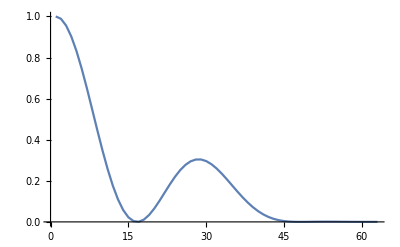

```mathematica
u[θ_] := Subscript[Ry, 3][θ] Subscript[C, 3][Subscript[Rz, 2][θ]] Subscript[Ry, 3][θ] 

ListLinePlot @  Table[
	CalcFidelity[ψ, ApplyCircuit[u[θ],ψ,ϕ]],
	{θ, 0, 2π, .1}
]
```

```mathematica
DestroyQureg[ψ];
DestroyQureg[ϕ];
```

```mathematica
Uninstall["quest_link"];
```